```mathematica
SetDirectory["/Users/thongle/Desktop/WorkwithDan/MatrixChain/mathematica"];
<< MCMPackage`
```

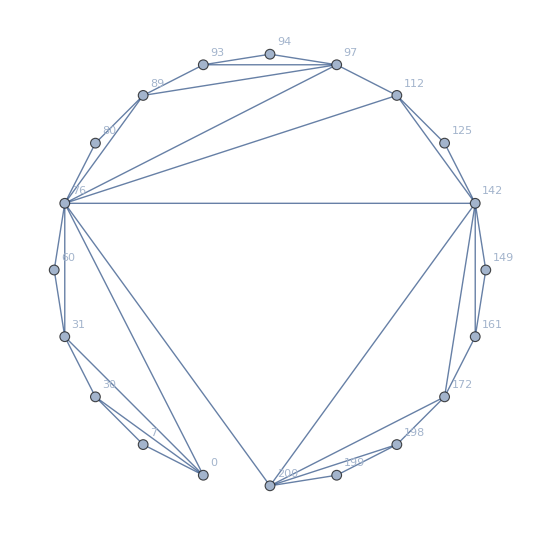

```mathematica
cuts = {0,7,30,31,60,76,80,89,93,94,97,112,125,142,149,161,172,198,199,200};
p = "((((A1A2)A3)(A4A5))(((((A6A7)(A8(A9A10)))A11)(A12A13))(((A14A15)A16)(A17(A18A19)))))";
NestedParenthesesToTriangulatedPolygonwithLabel[p, cuts]
```

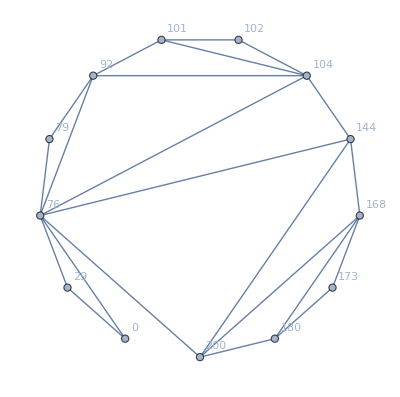

```mathematica
cuts = {0,29,76,79,92,101,102,104,144,168,173,180,200};
p = "((A1A2)((((A3A4)(A5(A6A7)))A8)(A9((A10A11)A12))))";
NestedParenthesesToTriangulatedPolygonwithLabel[p, cuts]
```

((A1(A2((A3A4)(A5(A6A7)))))((A8(A9((A10A11)(A12A13))))(((A14A15)A16)A17)))

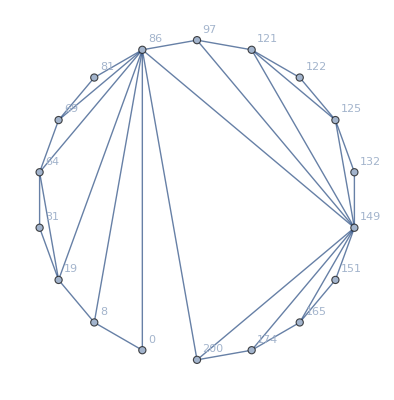

```mathematica
cuts = {0,8,19,31,64,69,81,86,97,121,122,125,132,149,151,165,174,200};
p = "((A1(A2((A3A4)(A5(A6A7)))))((A8(A9((A10A11)(A12A13))))(((A14A15)A16)A17)))"
NestedParenthesesToTriangulatedPolygonwithLabel[p, cuts]
```

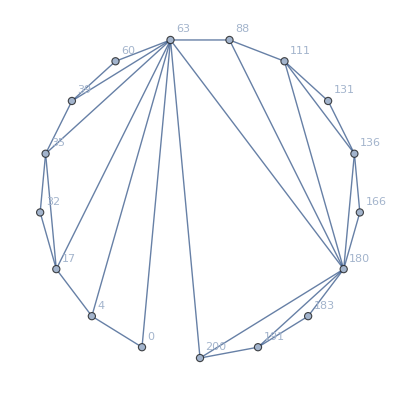

```mathematica
cuts = {0,4,17,32,35,39,60,63,88,111,131,136,166,180,183,191,200};
p ="((A1(A2((A3A4)(A5(A6A7)))))((A8(A9((A10A11)(A12A13))))((A14A15)A16)))";
NestedParenthesesToTriangulatedPolygonwithLabel[p, cuts]
```

{0,5,13,19,40,65,66,67,80,88,107,117,123,186,195,200}

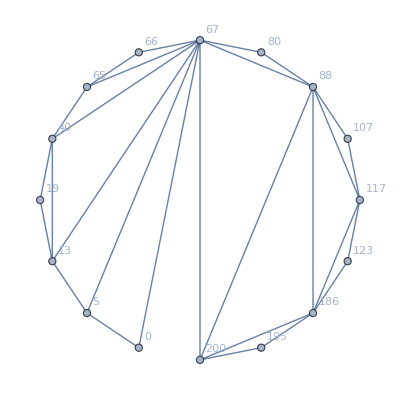

```mathematica
cuts = {0,5,13,19,40,65,66,67,80,88,107,117,123,186,195,200}
p = "((A1(A2((A3A4)(A5(A6A7)))))((A8A9)(((A10A11)(A12A13))(A14A15))))";
NestedParenthesesToTriangulatedPolygonwithLabel[p, cuts]
```

((A1(A2((A3A4)(A5(A6A7)))))(A8(A9((A10A11)(A12(A13A14))))))

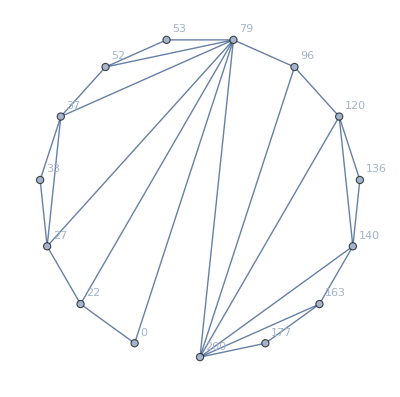

```mathematica
cuts = {0,22,27,33,37,52,53,79,96,120,136,140,163,177,200};
p = "((A1(A2((A3A4)(A5(A6A7)))))(A8(A9((A10A11)(A12(A13A14))))))"
NestedParenthesesToTriangulatedPolygonwithLabel[p, cuts]
```

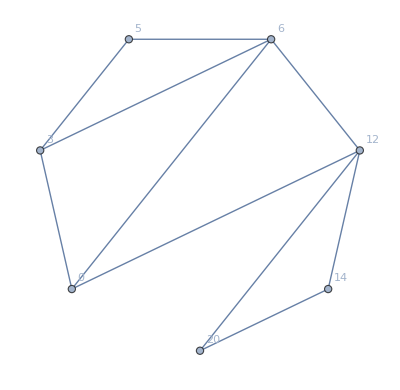

```mathematica
cuts = {0,3,5,6,12,14,20};
p = "(((A1(A2A3))A4)(A5A6))";
NestedParenthesesToTriangulatedPolygonwithLabel[p, cuts]
```

```mathematica
8 + 12 + 9 + 7
```

36